## Import numerical data

```mathematica
(* import τ as a function of q *)
τq1=Import[NotebookDirectory[]<>"data/tauqpsi_rho_1.dat"];
τq09=Import[NotebookDirectory[]<>"data/tauqpsi_rho_09.dat"];
τq08=Import[NotebookDirectory[]<>"data/tauqpsi_rho_08.dat"];
τq07=Import[NotebookDirectory[]<>"data/tauqpsi_rho_07.dat"];
τq06=Import[NotebookDirectory[]<>"data/tauqpsi_rho_06.dat"];
τq05=Import[NotebookDirectory[]<>"data/tauqpsi_rho_05.dat"];
τq04=Import[NotebookDirectory[]<>"data/tauqpsi_rho_04.dat"];
τq03=Import[NotebookDirectory[]<>"data/tauqpsi_rho_03.dat"];
τq02=Import[NotebookDirectory[]<>"data/tauqpsi_rho_02.dat"];
τq01=Import[NotebookDirectory[]<>"data/tauqpsi_rho_01.dat"];
```

```mathematica
τs={τq1,τq09,τq08,τq07,τq06,τq05,τq04,τq03,τq02,τq01};
```

## Legendre transform of τ_q ⟶ f-α graph

```mathematica
legendre[τq_]:=Block[{τinterp,α},
τinterp=Interpolation[τq];
α[q_]:=τinterp'[q];
{α[q],q α[q]-τinterp[q]}
]
```

```mathematica
fαs=legendre/@τs;
```

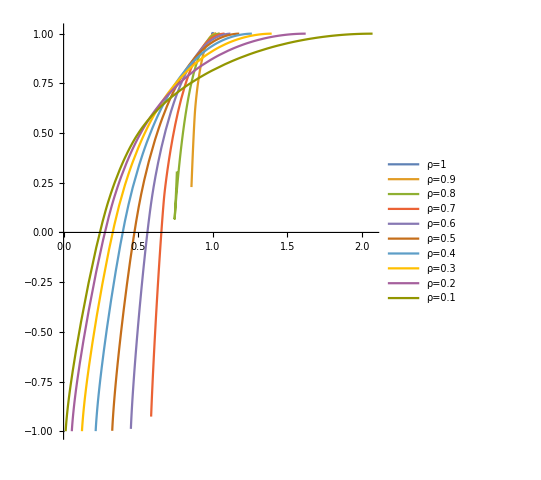

```mathematica
ParametricPlot[fαs,{q,0,20},AspectRatio->1.2,PlotRange->All,PlotLegends->("ρ="<>ToString[#]&/@{1,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1})]
```

## Theoretical implicit equation for τ_q, f-α

```mathematica
ω=(√5-1)/2//N;
(* interference factor *)
gam[ρ_,q_]:=1/(1+ρ^q);
(* molecular and atomic renormalization factors *)
lambp[ρ_]:=((1+gam[ρ,1.] ρ^2-√(1+(gam[ρ,1.] ρ^2)^2))/(2gam[ρ,1.] ρ^2))^-1;
barlambp[ρ_]:=((√((1+ρ^2)^4+4 ρ^4)-(1+ρ^2)^2)/(2 ρ^4))^-1;
(* q-weights for molecular and atomic levels *)
Cm[q_,τq_,ρ_]:=(2+(3-2ω)gam[ρ,q] ρ^(2q))ω^(-2τq)+gam[ρ,q] ρ^(2q)(ω^3/barlambp[ρ]^q ω^(-5τq)-(4 ω^2)/lambp[ρ]^q ω^(-4τq));
Ca[q_,τq_,ρ_]:=(1+2 ρ^(2q)+(3-2ω)ρ^(4q))ω^(-3τq)+ρ^(4q)(ω^3/barlambp[ρ]^q ω^(-6τq)-(4 ω^2)/lambp[ρ]^q ω^(-5τq));
(* implicit equation for the fractal dimensions *)
eq[q_,τq_,ρ_]:=(2 ω^2)/lambp[ρ]^q Cm[q,τq,ρ]+ω^3/barlambp[ρ]^q Ca[q,τq,ρ]-1;
(* find Subscript[τ, q] solving the implicit equation *)
implicitTau[q_,ρ_]:=τ/.FindRoot[eq[q,τ,ρ],{τ,q-1}];
```

## Theoretical prediction for τ_q, f-α

```mathematica
legendreTh[ρ_,qmin_,qmax_]:=Block[{τinterp,α},
τinterp=Interpolation[Table[{q,implicitTau[q,ρ]},{q,qmin,qmax,.01}]];
α[q_]:=τinterp'[q];
{α[q],q α[q]-τinterp[q]}
]
```

```mathematica
fα01th=legendreTh[0.1,-10,20];
```

```mathematica
fα02th=legendreTh[0.2,-10,20];
```

```mathematica
fα03th=legendreTh[0.3,-10,20];
```

```mathematica
fα04th=legendreTh[0.4,-10,20];
```

```mathematica
fα05th=legendreTh[0.5,-10,20];
```

```mathematica
fα06th=legendreTh[0.6,-10,20];
```

```mathematica
fα07th=legendreTh[0.7,-10,20];
```

```mathematica
fα08th=legendreTh[0.8,-10,20];
```

```mathematica
fα09th=legendreTh[0.9,-10,20];
```

```mathematica
fα1th=legendreTh[1.,-10,20];
```

```mathematica
fαsth={fα1th,fα09th,fα08th,fα07th,fα06th,fα05th,fα04th,fα03th,fα02th,fα01th};
```

```mathematica
plot[f1_,f2_,c_,ρ_]:=Show[{ParametricPlot[f1,{q,-10,20},PlotStyle->{ColorData[97,"ColorList"][[c]]},PlotLegends->{"ρ="<>ToString[ρ]}],ParametricPlot[f2,{q,0,20},PlotStyle->{Black,Dashed}]}]
```

```mathematica
p1=plot[fαsth[[10]],fαs[[10]],1,0.1];
```

```mathematica
p2=plot[fαsth[[9]],fαs[[9]],2,0.2];
```

```mathematica
p3=plot[fαsth[[8]],fαs[[8]],3,0.3];
```

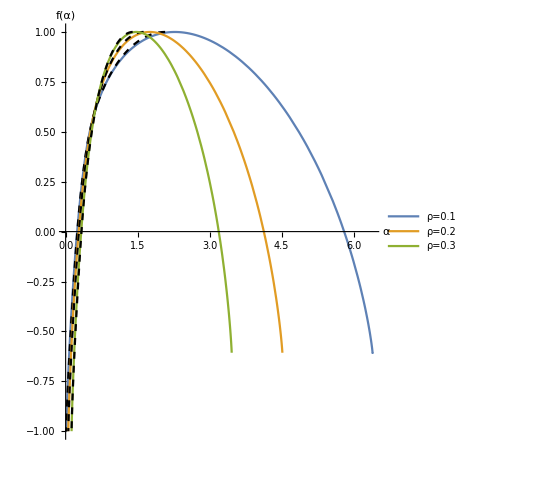

```mathematica
Show[{p1,p2,p3}, AspectRatio->1.2,AxesLabel->{"α","f(α)"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/f-alpha_01_to_03.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/f-alpha_01_to_03.pdf

```mathematica
p4=plot[fαsth[[7]],fαs[[7]],1,0.4];
```

```mathematica
p5=plot[fαsth[[6]],fαs[[6]],2,0.5];
```

```mathematica
p6=plot[fαsth[[5]],fαs[[5]],3,0.6];
```

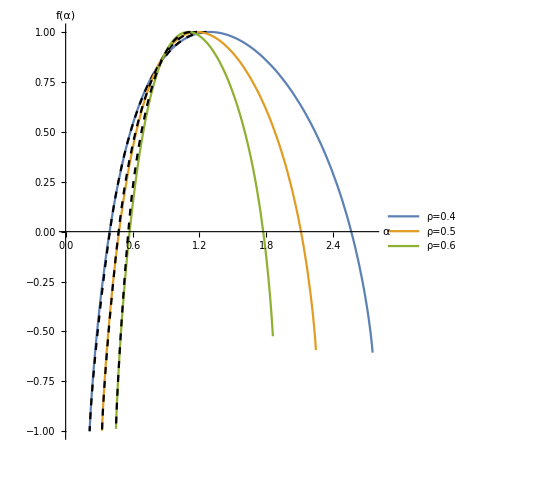

```mathematica
Show[{p4,p5,p6}, AspectRatio->1.2,AxesLabel->{"α","f(α)"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/f-alpha_04_to_06.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/f-alpha_04_to_06.pdf

```mathematica
p7=plot[fαsth[[4]],fαs[[4]],1,0.7];
```

```mathematica
p8=plot[fαsth[[3]],fαs[[3]],2,0.8];
```

```mathematica
p9=plot[fαsth[[2]],fαs[[2]],3,0.9];
```

```mathematica
p10=plot[fαsth[[1]],fαs[[1]],4,1.];
```

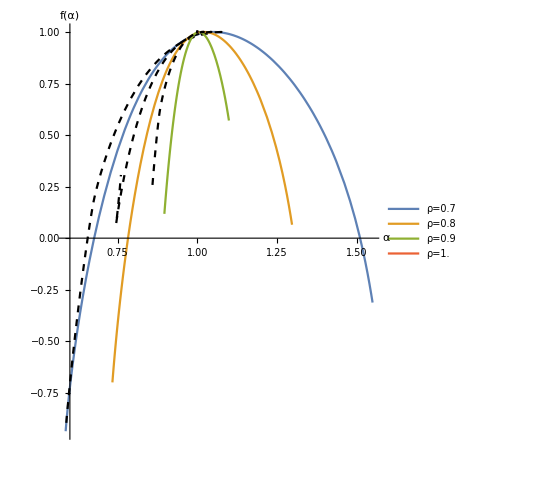

```mathematica
Show[{p7,p8,p9,p10}, AspectRatio->1.2,AxesLabel->{"α","f(α)"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/f-alpha_04_to_1.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/f-alpha_04_to_1.pdf